```mathematica
L1=SetPrecision[ 12.0326835814332, 15];
L2=SetPrecision[0.706873275327091, 15];
C1=SetPrecision[0.0000116279379708663, 15];
C2=SetPrecision[0.00001375304042498, 13];
R1=SetPrecision[118.128654394748, 15];
R2=SetPrecision[37.6544394679225, 15];
R3=SetPrecision[1078.5097577606, 14];
R4=SetPrecision[526.033775059273, 15];
dt=SetPrecision[0.0196349540849362, 15];
N1=8192;
t = dt * N1;

(*нахождение передаточной функции и ее АЧХ*)
Z1[w_] = R4 + 1/(I w C2);  (*первая ветвь параллельного соединения*)
Z2[w_]= 1/(I w C1)+R2 + I w L2 + R3; (*вторая ветвь параллельного соединения*)
```

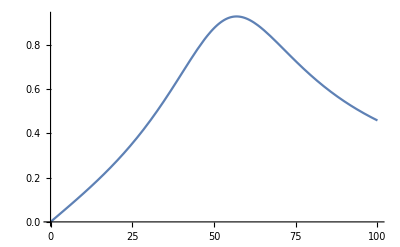

```mathematica
Zparalel[w_] = 1/(1/Z1[w]+1/Z2[w]); (*общий*)
I1[w_] = Uin/(R1 + I w L1 + Zparalel[w]);
Upar[w_] = I1[w] * Zparalel[w];
Ipar2[w_] = Upar[w]/Z2[w];
Uout[w_] = Ipar2[w] * R3;

H[w_]= Uout[w]/Uin;

Plot[Abs@H[w],{w, 0, 100}]
```

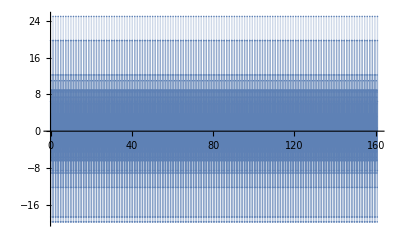

```mathematica
(*построение сигнала*)
signal = ReadList["C:\\Users\\Полина\\Desktop\\учеба\\foit\\idz3\\21.txt"];


ForPlot=Table[{(i-1)*dt, signal[[i]]},{i,1,N1}];
ListPlot[ForPlot, Filling->Axis,PlotRange->Full]
```

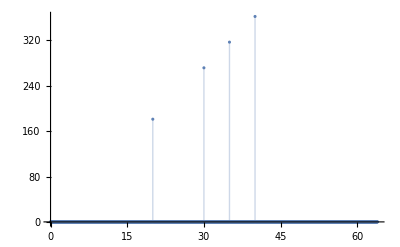

```mathematica
(*построение спектра*)
Fsig=Fourier[signal];
outN=Length@Fsig;
df=1/t;

FourAbs=Table[{2π df (i-1), Abs@Fsig[[i]]},{i,1,outN/5}];

ListPlot[FourAbs, Filling->Axis,PlotRange->Full]
```

0.66767659954

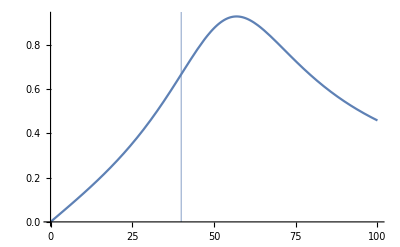

```mathematica
(*нахождение коэффициента усиления для четвертой гармоники*)
Abs@H[40]
Show[Plot[Abs@H[w],{w, 0, 100}], ListPlot[{{40, 3}}, Filling->Axis]]
```